## Tight binding of an extended SSH Model

## Lattice configuration

```mathematica
lattice[num_]:=Module[{atom1,atom2,t11,t12,t21,t22},atom1=Sphere[#,0.2]&/@Table[{x,0,0},{x,0,num}];
atom2=Sphere[#,0.2]&/@Table[{x+1/2,Sqrt[3]/2,0},{x,0,num}];
t11=Cylinder[#,0.05]&/@Table[{{x,0,0},{x+1/2,(√3)/2,0}},{x,0,num}];
t12=Cylinder[#,0.05]&/@Table[{{x+1/2,(√3)/2,0},{x+1,0,0}},{x,0,num-1}];
t21=Cylinder[#,0.05]&/@Table[{{x,0,0},{x+3/2,(√3)/2,0}},{x,0,num-1}];
t22=Cylinder[#,0.05]&/@Table[{{x+1/2,(√3)/2,0},{x+4/2,0,0}},{x,0,num-2}];
Graphics3D[{Red,atom1,Green,atom2,Black,t11,Orange,t12,Blue,t21,LightCyan,t22},Boxed->False,ViewPoint->Above]]
lattice[7]
```

-Graphics3D-

## Bulk Hamiltonian

```mathematica
hamiltonian[kx_,w_]:=Module[{t11,t12,t21,t22,h12,h21,ham},
t11=-1+w;
t12=-1-w;
t21=t2+ww;
t22=t2-ww;
h12=t11+t12*Exp[-ⅈ kx]+t21*Exp[-2ⅈ kx]+t22*Exp[ⅈ kx];
h21=Conjugate[h12];
ham={{0,h12},{h21,0}};
Return[ham];
]
```

```mathematica
el=ParallelTable[Eigenvalues[hamiltonian[kx,-0.5]/.{kx->kk,t2->-5,ww->-2.5}],{kk,-π,π,0.01π}];
```

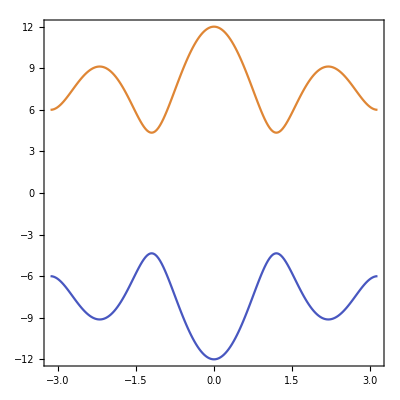

```mathematica
ListPlot[Transpose@Re[el],Joined->True,DataRange->{-π,π},AspectRatio->1,Frame->True,ColorFunction->"Rainbow"]
```

## Phase Diagram (Coarse)

```mathematica
Clear[h,t11,t12,t21,t22];
```

```mathematica
h[kx_]:=Module[{t11,t12,t21,t22,h12},
t11=-1+w;t12=-1-w;
t21=t2+ww;t22=t2-ww;
h12=t11+t12*Exp[-ⅈ kx]+t21*Exp[-2ⅈ kx]+t22*Exp[ⅈ kx];
Return[h12];
]
```

```mathematica
fun[kx_]:=Module[{f1},
f1=Log@h[kx];
Return[D[f1,kx]];
]
fun[kx]
```

(-ⅈ ⅇ^(-ⅈ kx) (-1-w)+ⅈ ⅇ^(ⅈ kx) (t2-ww)-2 ⅈ ⅇ^(-2 ⅈ kx) (t2+ww))/(-1+ⅇ^(-ⅈ kx) (-1-w)+w+ⅇ^(ⅈ kx) (t2-ww)+ⅇ^(-2 ⅈ kx) (t2+ww))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in kx near {kx} = {5.94443×10^-6}. NIntegrate obtained 9.0834+1.50193 ⅈ and 4.83451 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in kx near {kx} = {1.57079}. NIntegrate obtained -3.88889-3.17907 ⅈ and 6.07903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in kx near {kx} = {5.94443×10^-6}. NIntegrate obtained 9.06652+1.53962 ⅈ and 4.94151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in kx near {kx} = {5.94443×10^-6}. NIntegrate obtained 9.05886+1.54465 ⅈ and 4.65927 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

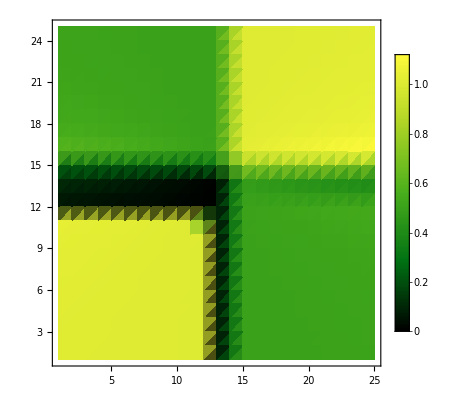

-1

```mathematica
ListDensityPlot[ParallelTable[Abs@Re[NIntegrate[fun[kx]/.{w->-0.5,t2->t,ww->δ},{kx,-π,π,0.05},AccuracyGoal->5,MaxRecursion->20]/(2π ⅈ)],{t,-6,6,0.5},{δ,-6,6,0.5}],PlotTheme->"Business",ColorFunction->"AvocadoColors"]
Round@Re[NIntegrate[fun[kx]/.{w->-0.5,t2->-5,ww->-2.5},{kx,-π,π,0.05}]/(2π ⅈ)]
```

## Winding Pattern

```mathematica
d[kx_,w_]:=Module[{dx,dy},
dx=Re@ComplexExpand@hamiltonian[kx,w][[1,2]];
dy=Im@ComplexExpand@hamiltonian[kx,w][[1,2]];
Return[{dx,dy}];
]
```

```mathematica
contr1=Flatten[#,1]&@ParallelTable[List@d[kx,-0.5]/.{kx->kk,t2->-5,ww->-2.5},{kk,0,2*π,0.01π}];
contr2=Flatten[#,1]&@ParallelTable[List@d[kx,0]/.{kx->kk,t2->-5,ww->-1.5},{kk,0,2*π,0.01π}];
contr3=Flatten[#,1]&@ParallelTable[List@d[kx,0.5]/.{kx->kk,t2->-5,ww->-0},{kk,0,2*π,0.01π}];
```

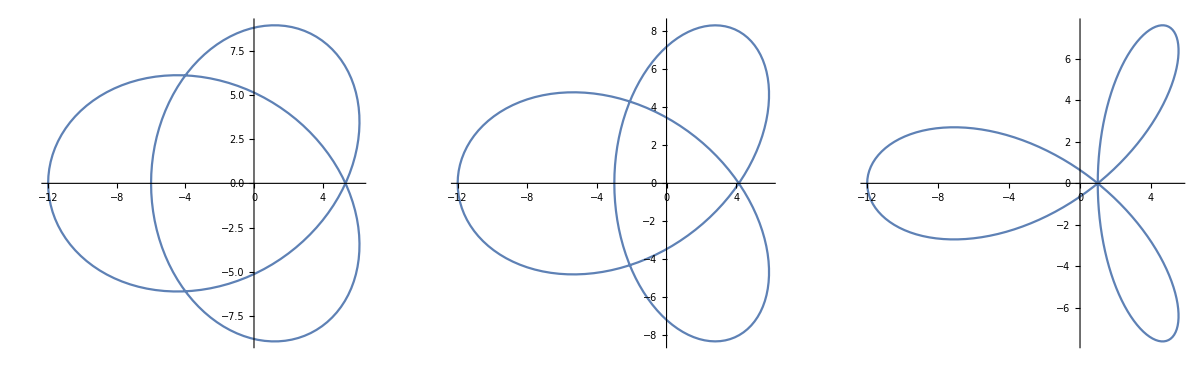

```mathematica
GraphicsRow@{ListPlot[contr1,Joined->True,AspectRatio->1,PlotStyle->PointSize[Large]],ListPlot[contr2,Joined->True,AspectRatio->1,PlotStyle->PointSize[Large]],ListPlot[contr3,Joined->True,AspectRatio->1,PlotStyle->PointSize[Large]]}
```

## Edge State

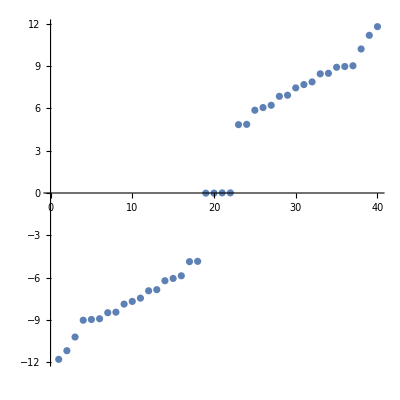

```mathematica
hamiltonianFinite[num_]:=Module[{t11,t12,t21,t22,hamUp,hamDown,ham},
t11=-1+w;
t12=-1-w;
t21=t2+ww;
t22=t2-ww;
hamUp=KroneckerProduct[DiagonalMatrix[Table[1,num-1],1],{{0,t12},{t22,0}}]+KroneckerProduct[DiagonalMatrix[Table[1,num-2],2],{{0,t21},{0,0}}];
hamDown=KroneckerProduct[DiagonalMatrix[Table[1,num-1],-1],{{0,t22},{t12,0}}]+KroneckerProduct[DiagonalMatrix[Table[1,num-2],-2],{{0,0},{t21,0}}];
ham = hamUp+hamDown+KroneckerProduct[IdentityMatrix[num],{{0,t11},{t11,0}}];
Return[ham];
]
hFinite=hamiltonianFinite[20]//Normal;
el=Sort@Eigenvalues[hFinite/.{w->-0.5,ww->-2.5,t2->-5}];
ListPlot[el,AspectRatio->1]
```